```mathematica
findRoots[expr_,ϵ_Symbol,rootEstimates_List,print_?BooleanQ,maxIteration_Integer:1000]:=
Module[
{numberOfRoots,zeros,rootEstimate,sol,zero},
numberOfRoots=Length[rootEstimates];
zeros={};
For[n=0,n<numberOfRoots,n++,
rootEstimate=rootEstimates[[n+1]];
sol=Quiet[FindRoot[expr==0,{ϵ,rootEstimate},MaxIterations->1000],{FindRoot::lstol}];
zero=Re[{ϵ,0}/.sol];
If[print,
Print["Estimated Root: ",rootEstimate,", Calculated Root: ",zero];
];
zeros=Append[zeros,zero];
];
Return[zeros];
]
```

```mathematica
U[a_,x_]:=ParabolicCylinderD[-a-1/2,x]
```

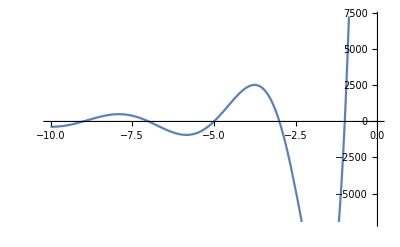

```mathematica
Plot[U[1/2*a,Sqrt[2]*-5],{a,-10,0}]
```

```mathematica
rootEstimates=Table[{-(2n+1)},{n,0,100}];
ruts=findRoots[U[1/2*a,Sqrt[2]*-5],a,rootEstimates,False];
```

```mathematica
roots=Flatten[ruts[[All,1]]];
```

```mathematica
rt={};
For[n=2,n≤Length[roots],n++,
If[Abs[roots[[n]] - roots[[n-1]]]≠0,
rt=Append[rt,roots[[n]]];
];
];
```

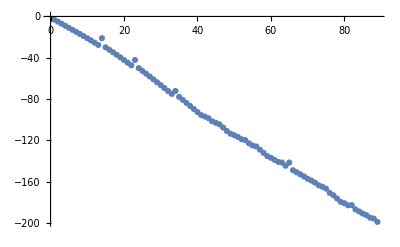

```mathematica
ListPlot[rt]
```

```mathematica
Fit[rt,{x},x]
```

-2.24966 x

```mathematica
S={};
For[n=2,n<=Length[roots],n++,
S=Append[S,roots[[n]]-roots[[n-1]]];
];
```

```mathematica
A={};
For[n=1,n≤Length[S],n++,
If[S[[n]]<0,
A=Append[A,S[[n]]]];
]
```

```mathematica
For[n=1,n≤Length[A],n++,
If[A[[n]]≤-4||A[[n]]>=-2,
A=Delete[A,n];
];
];
```

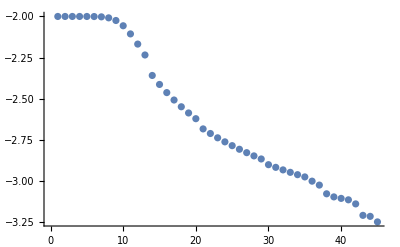

```mathematica
ListPlot[A]
```